{{Phi[η]→(ⅇ^(1/2 ⅈ m η^2) C[1] HypergeometricU[-(ⅈ k^2)/(4 m),0,-ⅈ m η^2])/η^2+(ⅇ^(1/2 ⅈ m η^2) C[2] LaguerreL[(ⅈ k^2)/(4 m),-1,-ⅈ m η^2])/η^2}}

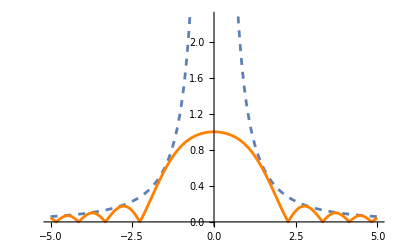

```mathematica
(* Near the Bang: a\proto \eta*)
Clear[Phi, eqPhi]
eqPhi=Phi''[η]+3Phi'[η]/η+(k^2+m^2η^2)Phi[η]==0;
DSolve[eqPhi,Phi[η],η]
Plot[{Abs[(ⅇ^(1/2 ⅈ m η^2) HypergeometricU[-(ⅈ k^2)/(4 m),0,-ⅈ m η^2])/η^2]/.{k->1,m->1},Abs[(ⅇ^(1/2 ⅈ m η^2) LaguerreL[(ⅈ k^2)/(4 m),-1,-ⅈ m η^2])/η^2]/.{k->1,m->1}},{η,-5,5}, PlotStyle->{Dashed, Orange}]
```

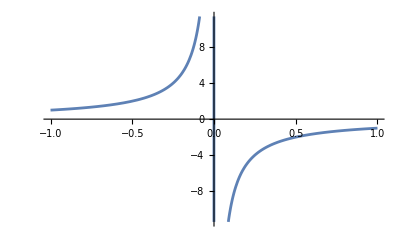

{{Phi[η]→(BesselJ[√((-m^2+λ)/λ),k η-k ηtot] C[1])/(-η+ηtot)+(BesselY[√((-m^2+λ)/λ),k η-k ηtot] C[2])/(-η+ηtot)}}

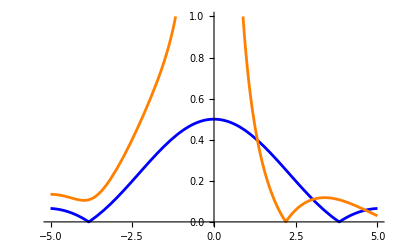

```mathematica
(* Near FCB: a=1/Sqrt[λ]/(ηtot-η))*)
Clear[Phi, eqPhi,λ,ηtot]
Plot[1/Sqrt[λ]/(ηtot-η)/.{λ->1,ηtot->0},{η,-1,1}]
eqPhi=Phi''[η]-3/(ηtot-η)Phi'[η]+(k^2+m^2/λ/(ηtot-η)^2)Phi[η]==0;
DSolve[{eqPhi},Phi[η],η]
Plot[{Abs[BesselJ[√((-m^2+λ)/λ),k η-k ηtot]/(-η+ηtot)]/.{k->1,m->0.001,λ->1,ηtot->0},Abs[BesselY[√((-m^2+λ)/λ),k η-k ηtot]/(-η+ηtot)]/.{k->1,m->0.001,λ->1,ηtot->0}},{η,ηtot-5,ηtot+5}/.{ηtot->0}, PlotStyle->{Blue, Orange},PlotRange->{Automatic,{0,1}}]
```

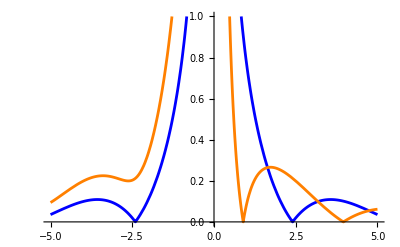

```mathematica
Plot[{Abs[BesselJ[√((-m^2+λ)/λ),k η-k ηtot]/(-η+ηtot)]/.{k->1,m->1,λ->1,ηtot->0},Abs[BesselY[√((-m^2+λ)/λ),k η-k ηtot]/(-η+ηtot)]/.{k->1,m->1,λ->1,ηtot->0}},{η,ηtot-5,ηtot+5}/.{ηtot->0}, PlotStyle->{Blue, Orange},PlotRange->{Automatic,{0,1}}]
```